# QEA Project 1: Boat Design

## Quantitative Engineering Analysis Project 1

Sparsh Bansal, Chris Lee

## Boat Design - Sparistopher

#### In this section, we define (in this order) (i) The curves which comprise the shape of the hull of our boat, (ii) The waterline with respect to the boat, (iii) The region of the boat that is under the water, and (iv) A function for analysis of the hull design - the variations of the waterline in terms of the draft and the waterline angle.

```mathematica
boat1=ImplicitRegion[-14≤x≤14&&-(x/3+1.5)^3+Abs[(((z)/11)^4)]≤y≤12&&-28≤z≤28,{x,y,z}];
boat2=ImplicitRegion[-14≤x≤14&&(x/3-1.5)^3+Abs[(((z)/11)^4)]≤y≤12&&-28≤z≤28,{x,y,z}];
boat=RegionIntersection[boat1,boat2]
water = ImplicitRegion[y<Tan[θ Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}]
under=RegionIntersection[boat,water]
Manipulate[RegionPlot3D[{under/.{d->dd,θ->θθ},water/.{d->dd,θ->θθ},boat},AspectRatio->Automatic, PlotTheme->"Scientific",AxesLabel->{x,y,z}],{{dd,1,"Waterline draft"},-5,20,Appearance->"Labeled"},{{θθ,1,"Waterline Angle"},0,180,Appearance->"Labeled"}]
```

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/14641≤y≤12&&-0.037037 (4.5+x)^3+z^4/14641≤y≤12,{x,y,z}]

ImplicitRegion[y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/14641≤y≤12&&-0.037037 (4.5+x)^3+z^4/14641≤y≤12&&y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

```mathematica
boat1=ImplicitRegion[-14≤x≤14&&-(x/3+1.5)^3+Abs[(((z)/11)^4)]≤y≤12&&-28≤z≤28,{x,y,z}];
boat2=ImplicitRegion[-14≤x≤14&&(x/3-1.5)^3+Abs[(((z)/11)^4)]≤y≤12&&-28≤z≤28,{x,y,z}];
boat=RegionIntersection[boat1,boat2]
water = ImplicitRegion[y<Tan[θ Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}]
under=RegionIntersection[boat,water]
Manipulate[RegionPlot3D[{under/.{d->dd,θ->θθ},water/.{d->dd,θ->θθ},boat},AspectRatio->Automatic, PlotTheme->"Scientific",AxesLabel->{x,y,z}],{{dd,1,"Waterline draft"},-5,20,Appearance->"Labeled"},{{θθ,1,"Waterline Angle"},0,180,Appearance->"Labeled"}]
```

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/14641≤y≤12&&-0.037037 (4.5+x)^3+z^4/14641≤y≤12,{x,y,z}]

ImplicitRegion[y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/14641≤y≤12&&-0.037037 (4.5+x)^3+z^4/14641≤y≤12&&y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

```mathematica
boat1=ImplicitRegion[-14≤x≤14&&-(x/3+1.5)^3+Abs[(((z)/11)^4)]≤y≤12&&-28≤z≤28,{x,y,z}];
boat2=ImplicitRegion[-14≤x≤14&&(x/3-1.5)^3+Abs[(((z)/11)^4)]≤y≤12&&-28≤z≤28,{x,y,z}];
boat=RegionIntersection[boat1,boat2]
water = ImplicitRegion[y<Tan[θ Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}]
under=RegionIntersection[boat,water]
Manipulate[RegionPlot3D[{under/.{d->dd,θ->θθ},water/.{d->dd,θ->θθ},boat},AspectRatio->Automatic, PlotTheme->"Scientific",AxesLabel->{x,y,z}],{{dd,1,"Waterline draft"},-5,20,Appearance->"Labeled"},{{θθ,1,"Waterline Angle"},0,180,Appearance->"Labeled"}]
```

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/14641≤y≤12&&-0.037037 (4.5+x)^3+z^4/14641≤y≤12,{x,y,z}]

ImplicitRegion[y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

ImplicitRegion[-28≤z≤28&&-14≤x≤14&&0.037037 (-4.5+x)^3+z^4/14641≤y≤12&&-0.037037 (4.5+x)^3+z^4/14641≤y≤12&&y<d+x Tan[° θ]&&-15<x<15&&-30<y<100&&-30≤z≤30,{x,y,z}]

```mathematica
(* Test Plotter *)
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],
ListPointPlot3D[{{0,1.72755,0}}, PlotStyle->Directive[Green,Opacity[1]]]]
```

-Graphics3D-

#### In this section, we plot the Center of Mass and Center of Buoyancy on a 3D plot of our boat for several heel angles: 0 Degree

Green Label - COM
Black Label - COB

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y<Tan[0 Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->0}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->0}]
```

3.04709

{-5.97325×10^-17,1.41403,-2.55604×10^-7}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->0}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### 30 Degree

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y<Tan[30 Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->30}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->30}]
```

2.01655

{4.27488,2.51152,-5.48583×10^-17}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->30}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### 60 Degree

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y<Tan[60 Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->60}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->60}]
```

-3.91481

{7.46538,5.78314,-4.25666×10^-16}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->60}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### 120 Degree

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y>Tan[120 Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->120}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->120}]
```

17.7406

{7.66226,9.05742,-4.78493×10^-17}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->120}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### 130 Degree

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y>Tan[130Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->130}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->130}]
```

14.7071

{7.41353,9.41234,-1.13808×10^-16}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->130}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### 150 Degree

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y>Tan[150Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->150}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->150}]
```

11.6427

{6.59459,10.0814,-9.93713×10^-17}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->150}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### 180 Degree

```mathematica
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y>Tan[180Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->180}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]]
cob = RegionCentroid[under/.{d->draft,θ->180}]
```

10.4711

{-1.56094×10^-17,11.243,3.04664×10^-16}

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Red,Opacity[0.5]]],RegionPlot3D[water/.{d->draft,θ->180}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->100, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{{com}}, PlotStyle->Directive[Green,Opacity[1]]],
ListPointPlot3D[{{cob}}, PlotStyle->Directive[Black,Opacity[1]]]]
```

-Graphics3D-

#### In this section, we define the variables that we obtained from the SolidWorks Model of our boat: (i) Mass of the Boat (ii) COM of the Boat (iii) Mass of the Ballast (iv) The COM of the boat - ballast assembly (Calculated in Mathematica)

```mathematica
newcomcode[comballast_]:=Module[{},
massboat = 315;
comboat= {0,11.21,0};
massballast= 1000;
newcom=((massboat*comboat)+(massballast*comballast))/(massboat+massballast);
newcom
]
```

```mathematica
newcomcode[{0,0.7485,0}]
```

{0,3.25449,0}

#### In this section, we define the functions that we use to obtain the righting moment that is acting on the boat. Waterline Angle < 90 Degrees

```mathematica
Submergedless90[θθ_]:=Module[{},
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y<Tan[θθ Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->θθ}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft,θ->θθ}];
buoyancy = mass*980*{-Sin[θθ Degree],Cos[θθ Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

#### In this section, we define the functions that we use to obtain the righting moment that is acting on the boat. Waterline Angle > 90 Degrees

```mathematica
Submergedmore90[θθ_]:=Module[{},
mass= 1315;
com = {0,3.25,0};
water = ImplicitRegion[y>Tan[θθ Degree]*x+d&& -15<x<15&&-30<y<100&&-30<=z≤30,{x,y,z}];
under=RegionIntersection[boat,water];
disp=Integrate[1,{x,y,z}∈under/.{θ->θθ}];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft,θ->θθ}];
buoyancy = mass*980*{-Sin[θθ Degree],Cos[θθ Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

```mathematica
before90 = Table[{theta,Submergedless90[theta]},{theta,{0,10,20,30,40,50,60,70,80}}]
```

{{0,-7.69773×10^-11},{10,1.6118×10^6},{20,3.13069×10^6},{30,4.29512×10^6},{40,5.26508×10^6},{50,6.59151×10^6},{60,7.63742×10^6},{70,7.36941×10^6},{80,6.67464×10^6}}

```mathematica
after90 = Table[{theta,Submergedmore90[theta]},{theta,{100,110,120,130,140,150,160,170,180}}]
```

{{100,4.49229×10^6},{110,3.08922×10^6},{120,1.54417×10^6},{130,-57597.4},{140,-1.60825×10^6},{150,-2.95807×10^6},{160,-3.84148×10^6},{170,-3.37014×10^6},{180,2.01158×10^-11}}

#### In this section, we find and plot the results.

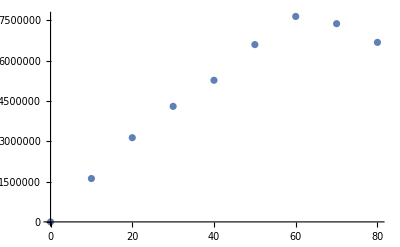

```mathematica
ListPlot[before90]
ListPlot[{{{0,-7.697731341238518*^-11},{10,1.6117969999596088*^6},{20,3.130685400111096*^6},{30,4.295119286440562*^6},{40,5.26508138860967*^6},{50,6.591513650189281*^6},{60,7.637417976334997*^6},{70,7.369406305421029*^6},{80,6.674636087897369*^6}}}]
```

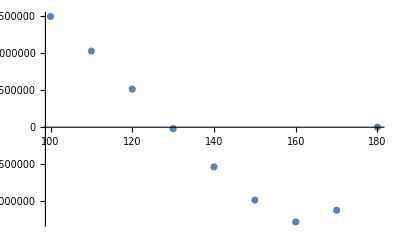

```mathematica
ListPlot[{{100,4.492285882425818*^6},{110,3.0892233977019624*^6},{120,1.5441742377184266*^6},{130,-57597.35070126683},{140,-1.6082452983155984*^6},{150,-2.958066348619032*^6},{160,-3.8414826675554756*^6},{170,-3.370135743164603*^6},{180,2.0115779159578246*^-11}}]
```

```mathematica
AVS = {{0,-7.697731341238518*^-11},{10,1.6117969999596088*^6},{20,3.130685400111096*^6},{30,4.295119286440562*^6},{40,5.26508138860967*^6},{50,6.591513650189281*^6},{60,7.637417976334997*^6},{70,7.369406305421029*^6},{80,6.674636087897369*^6},{100,4.492285882425818*^6},{110,3.0892233977019624*^6},{120,1.5441742377184266*^6},{130,-57597.35070126683},{140,-1.6082452983155984*^6},{150,-2.958066348619032*^6},{160,-3.8414826675554756*^6},{170,-3.370135743164603*^6},{180,2.0115779159578246*^-11}}
```

{{0,-7.69773×10^-11},{10,1.6118×10^6},{20,3.13069×10^6},{30,4.29512×10^6},{40,5.26508×10^6},{50,6.59151×10^6},{60,7.63742×10^6},{70,7.36941×10^6},{80,6.67464×10^6},{100,4.49229×10^6},{110,3.08922×10^6},{120,1.54417×10^6},{130,-57597.4},{140,-1.60825×10^6},{150,-2.95807×10^6},{160,-3.84148×10^6},{170,-3.37014×10^6},{180,2.01158×10^-11}}

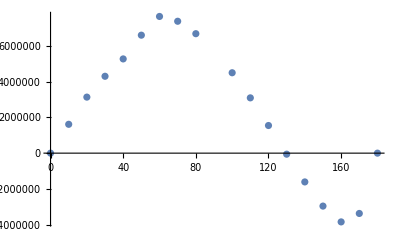

```mathematica
ListPlot[{{0,-7.697731341238518*^-11},{10,1.6117969999596088*^6},{20,3.130685400111096*^6},{30,4.295119286440562*^6},{40,5.26508138860967*^6},{50,6.591513650189281*^6},{60,7.637417976334997*^6},{70,7.369406305421029*^6},{80,6.674636087897369*^6},{100,4.492285882425818*^6},{110,3.0892233977019624*^6},{120,1.5441742377184266*^6},{130,-57597.35070126683},{140,-1.6082452983155984*^6},{150,-2.958066348619032*^6},{160,-3.8414826675554756*^6},{170,-3.370135743164603*^6},{180,2.0115779159578246*^-11}}]
```

F x+D x^2+C x^3+B x^4+A x^5

{{A},{B},{C},{D},{F}}

{A→0.000475537,B→-0.0485358,C→-12.8235,D→245.067,F→153503.}

153503. x+245.067 x^2-12.8235 x^3-0.0485358 x^4+0.000475537 x^5

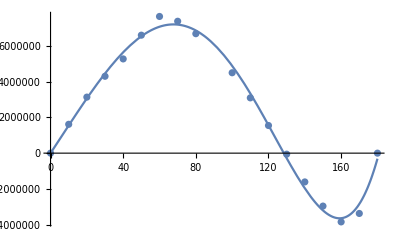

```mathematica
curve = A*x^5 + B*x^4+C*x^3+D*x^2+F*x
params = {{A},{B},{C},{D},{F}}
bestparams = FindFit[AVS,curve,params,x]
bestcurve = curve/.bestparams
Show[ListPlot[AVS],Plot[bestcurve,{x,0,180}]]
```

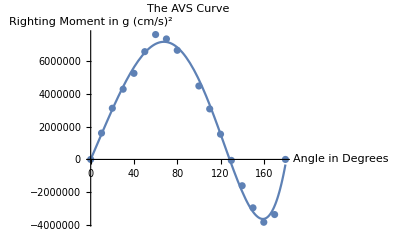

```mathematica
Show[%36,AxesLabel->{HoldForm[Angle in Degrees],HoldForm[Righting Moment in g (cm/s)^2]},PlotLabel->HoldForm[The AVS Curve],LabelStyle->{GrayLevel[0]}]
```

#### The analytical value of our AVS = 130 Degrees